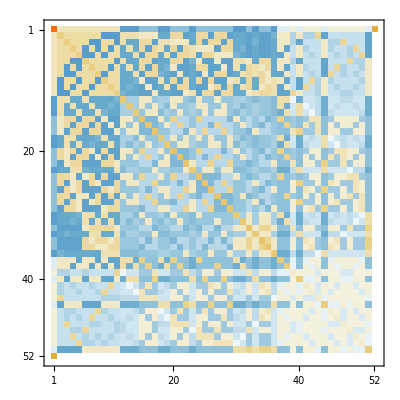

```mathematica
MatrixPlot[MapAll[Numerator,ConversionMatrix["C","F"]]//Inverse]
```

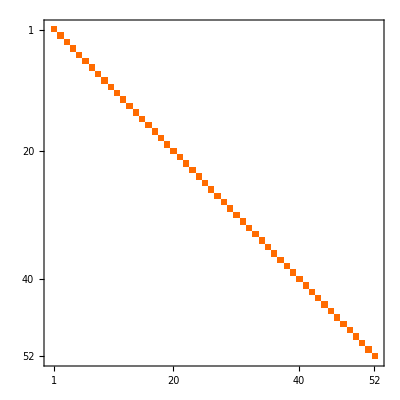
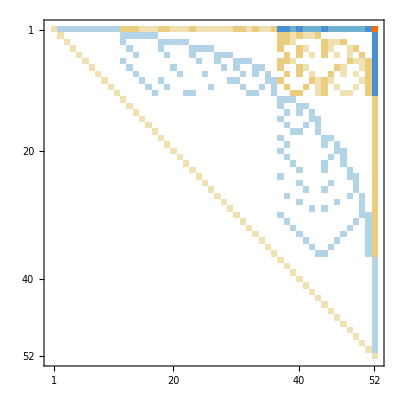
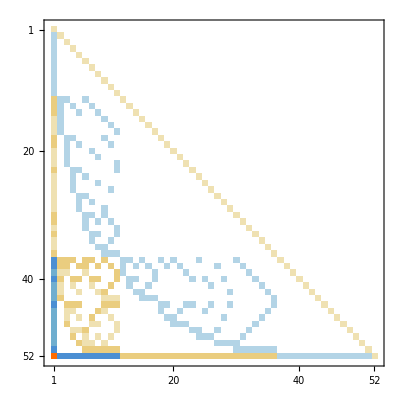
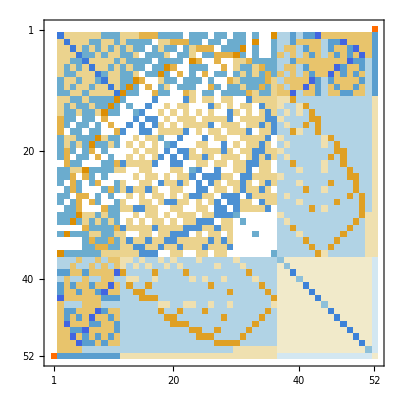
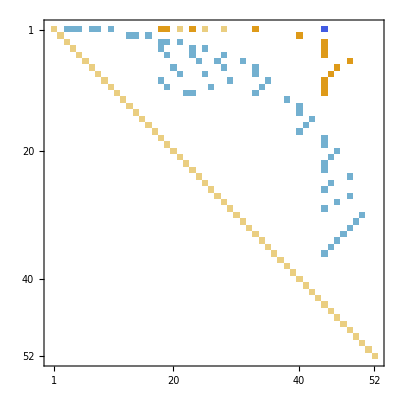
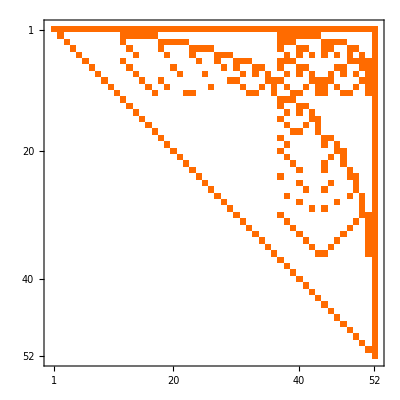
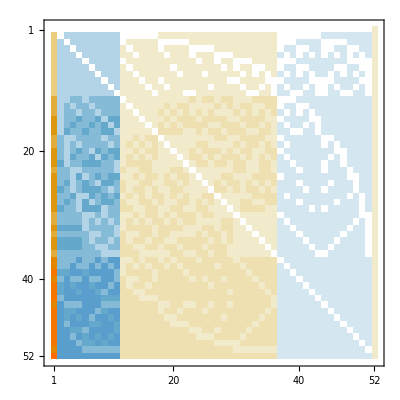
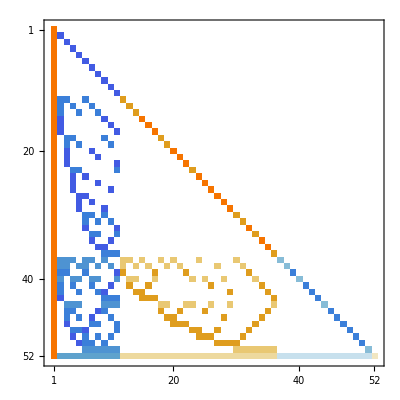
| C | E | G | F | T
C | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
F | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix[baseFrom,baseTo]], {baseFrom, allBases},{baseTo, allBases}], TableHeadings->{allBases,allBases}, TableAlignments->Center]
```

```mathematica
Multicolumn[With[{base="G"},Table[Framed[ShowGraph[allGraphs5,k]]->FormulaGraph[allGraphs5[k,"colofour"]],{k,Bases[base,"AtomKeys"]}]]]
```

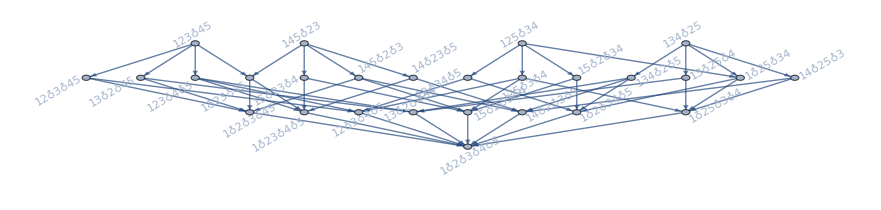

```mathematica
FormulaGraphReverse[allGraphs5[84,"colofour"]]
```